```mathematica
Hz[r_,z_,a_]:= Ic/(2π Q[r,z,a]^(1/2))(EllipticK[k[r,z,a]]+(a^2-r^2-z^2)/((1-k[r,z,a]^2)Q[r,z,a])EllipticE[k[r,z,a]])
Hr[r_,z_,a_]:=If[r>0, Ic/(2π Q[r,z,a]^(1/2))z/r(-EllipticK[k[r,z,a]]+(a^2+r^2+z^2)/((1-k[r,z,a]^2)Q[r,z,a])EllipticE[k[r,z,a]]),0]
Q[r_,z_,a_]:=(a+r)^2+z^2
k[r_,z_,a_]:=Sqrt[4 a r /Q[r,z,a]]
Ic=1;
```

```mathematica
Hr[0,3,1]
```

0

```mathematica
Manipulate[Plot[{Hz[a/10,z,a],Hr[.1,z,a]},{z,-1,2},PlotRange->{-.2,.2}],{a,.5,1}]
```

```mathematica
Plot3D[Hr[r,z,1],{r,0,1},{z,0,1},AxesLabel->{r,z,Hr}]
```

-Graphics3D-

```mathematica
afront=1;
aback=afront/4;
nloop=100;
length=2;
```

```mathematica
loop[x_,n_]:={Hr[x[[1]],x[[2]]-zstep[n],a[n]],0,Hz[x[[1]],x[[2]]-zstep[n],a[n]]}
a[n_]:=afront-(afront-aback) *n/nloop
zstep[n_]:=length * n /nloop
Htot[x_]:=Sum[loop[x,n],{n,0,nloop}]
```

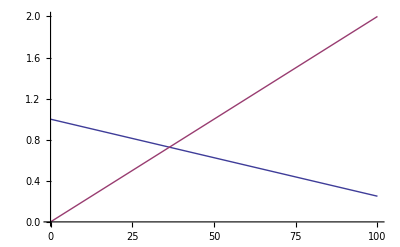

```mathematica
Plot[{a[n],zstep[n]},{n,0,nloop}]
```

```mathematica
Manipulate[Show[{Plot[loop[{0,z,0},n].{0,0,1},{z,-length,2length},PlotRange->{0,2.5}],Graphics[Circle[{zstep[n],0},{.1,2a[n]}]]}],{n,0,nloop,5}]
```

```mathematica
Manipulate[Show[{Plot[loop[{aback/10,z,0},n].{0,0,1},{z,-length,2length},PlotRange->{0,2.5}],Graphics[Circle[{zstep[n],0},{.1,2a[n]}]]}],{n,0,nloop,5}]
```

```mathematica
Manipulate[Show[{Plot[loop[{aback/10,z,0},n].{1,0,0},{z,-length,2length},PlotRange->{-.2,0}],Graphics[Circle[{zstep[n],0},{.1,.2 a[n]}]]}],{n,0,nloop,5}]
```

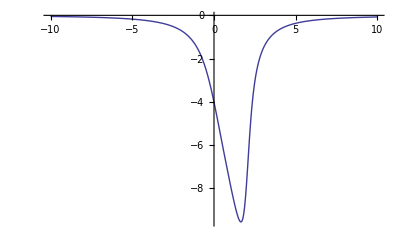

```mathematica
Plot[Htot[{aback/10,z,0}].{1,0,0},{z,-5length,5length},PlotRange->All]
```

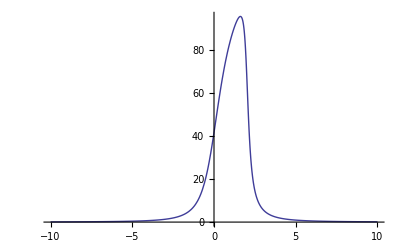

```mathematica
Plot[Htot[{aback/10,z,0}].{0,0,1},{z,-5length,5length},PlotRange->All]
```

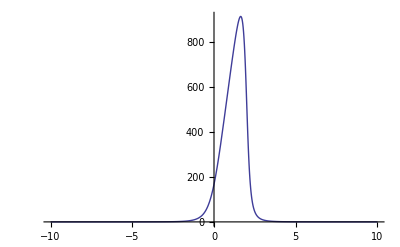

```mathematica
Plot[-Htot[{aback/10,z,0}].{0,0,1}*Htot[{aback/10,z,0}].{1,0,0},{z,-5length,5length},PlotRange->All]
```